# Warm Plasma Roots nx(nz) with Slab Profiles

## Open Additional files:

## Set Parameters by opening a Parameter Window Get dispersion routines by evaluating Disper_no_package.nb Get plotting and printing routines by evaluating PlotPack.nb

## First Do Cold Plasma again

### Plot Real and Imaginary parts of nx from 2nd order warm plasma dispersion relation (i.e. E_‖≡0)

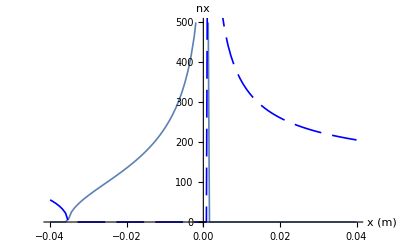

dataSet=Proto MPEX IC Kinetic Alfven

xProfileMin=-0.04

xProfileMax=0.04

nXmin=1.×10^19

nXmax=3.×10^19

BXmin=1.2

BXmax=1.2

freq=7.5

nz=127.324

etaList={0.,1.,0.,0.,0.}

xmin=-0.04

xmax=0.04

```mathematica
nPerpCold[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
     ColdDis0[freq,ne,b,nz,etaList]]
nt=Table[{x,nPerpCold[x]},{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexListPlot[nt,"x (m)","nx"]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of kx from 2nd order cold plasma dispersion relation (i.e. E_‖≡0)

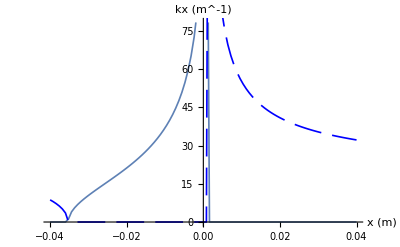

dataSet=Proto MPEX IC Kinetic Alfven

xProfileMin=-0.04

xProfileMax=0.04

nXmin=1.×10^19

nXmax=3.×10^19

BXmin=1.2

BXmax=1.2

freq=7.5

nz=127.324

etaList={0.,1.,0.,0.,0.}

xmin=-0.04

xmax=0.04

```mathematica
nPerpCold[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
     ColdDis0[freq,ne,b,nz,etaList]]
nt=Table[{x,k0 nPerpCold[x]},{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
ComplexListPlot[nt,"x (m)","kx (m^-1)"]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of nx from 4nd order cold plasma dispersion relation (i.e. fast and slow)

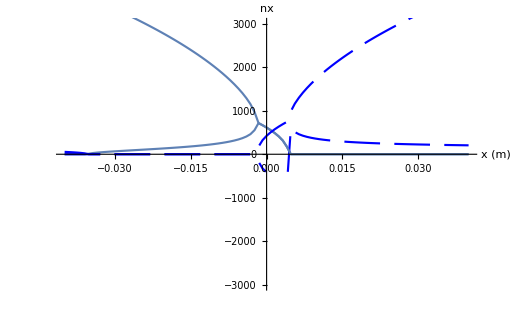

dataSet=Proto MPEX IC Kinetic Alfven

xProfileMin=-0.04

xProfileMax=0.04

nXmin=1.×10^19

nXmax=3.×10^19

BXmin=1.2

BXmax=1.2

freq=7.5

nz=127.324

etaList={0.,1.,0.,0.,0.}

xmin=-0.04

xmin=-0.04

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		ColdDis2FS[freq,ne,b,nz,etaList]]
nt2FS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=ComplexListPlot[nF,"x (m)","nx"];
g2=ComplexListPlot[nS,"x (m)","nx"];
Show[{g1,g2},PlotRange->{-3000.,3000}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmin}];
```

## Now Warm Plasma Stuff

### Plot Real and Imaginary parts of nx from 6th order warm plasma dispersion relation (expanded to 2nd order in k_⌊ρ)

```mathematica
nPerpWarm6[x_]:=Module[{ne,te,b,x0,TL},
		x0=x;
     ne=nprof[x0];
b=bprof[x0];
	  TL=tprof[x0] *TList;
	  WarmDis6[freq,ne,b,nz,etaList,TL]]
```

dataSet=Proto MPEX IC Kinetic Alfven

xProfileMin=-0.04

xProfileMax=0.04

nXmin=1.×10^19

nXmax=3.×10^19

BXmin=1.2

BXmax=1.2

freq=7.5

nz=127.324

etaList={0.,1.,0.,0.,0.}

TList={1.,0.,1.,0.,0.,0.}

xmin=-0.04

xmax=0.04

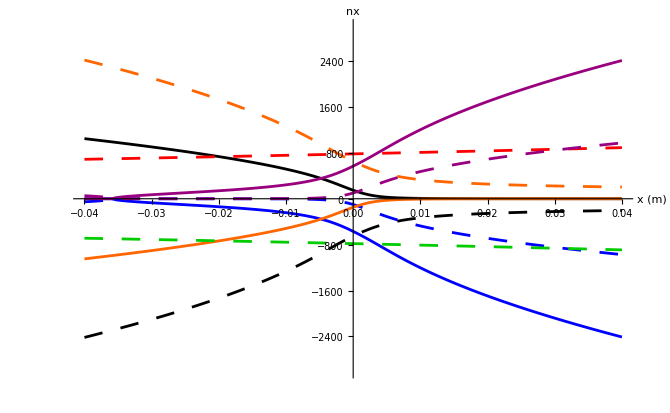

```mathematica
nxwarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
roots=rootSort[nxwarm];

g6=ComplexVectorListPlot[roots,"x (m)","nx"];
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TList, xmin,xmax}];
Show[g6,PlotRange->{-3000.,3000}]
```

Look close to where the modes cross

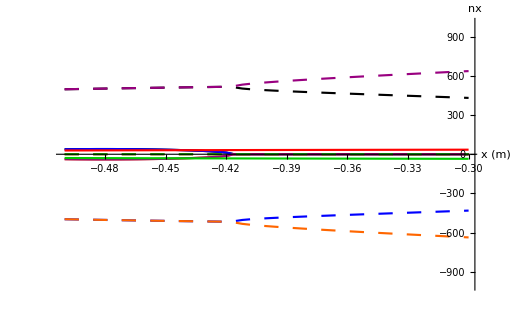

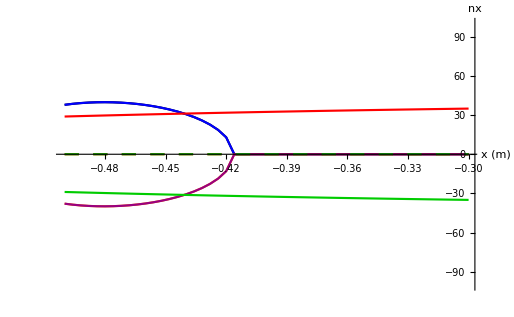

dataSet=DIII-D slab

xProfileMin=-0.68

xProfileMax=0

nXmin=3.×10^18

nXmax=3.×10^19

BXmin=1.35021

BXmax=1.9

freq=60

nz=2

etaList={1.,0.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

xmin=-0.5

xmax=-0.3

```mathematica
xmin=-0.5;
xmax=-0.3;
nxwarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
roots=rootSort[nxwarm];

g6=ComplexVectorListPlot[roots,"x (m)","nx"];
Show[g6,PlotRange->{-1000.,1000}]
Show[g6,PlotRange->{-100.,100}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TList, xmin,xmax}];
```

## Now Try with Hot Plasma Dispersion using root finder

```mathematica
nPerpHot[x_,nxGuess_]:=Module[{ne,tprof,b,x0,TL,nx0},
		x0=x;
nx0=nxGuess;
     ne=nprof[x0];
b=bprof[x0];
     TL=tprof[x0] *TList;
rootRule=FindRoot[DisFuncGeneral[freq,ne,b,nz,nx,etaList,TL,nminList,nmaxList,modelList],{nx,nx0}, MaxIterations->30];
nx/.rootRule]
```

### First try root finding on warm plasma dispersion rel (model = 1)

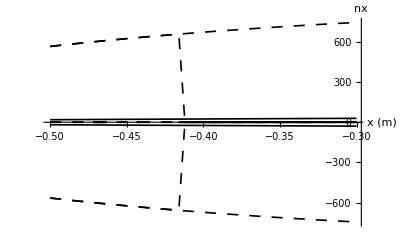

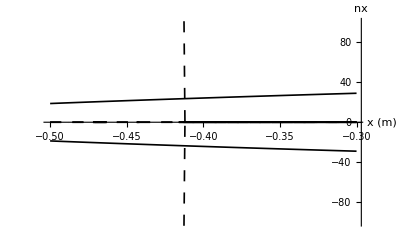

dataSet=DIII-D slab

xProfileMin=-0.68

xProfileMax=0

nXmin=3.×10^18

nXmax=3.×10^19

BXmin=1.35021

BXmax=1.9

freq=60

nz=2

etaList={1.,0.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modleList=modleList

xmin=-0.5

xmax=-0.3

```mathematica
nxhot[iRoot_]:=Module[{iRoot0,nxWarm,rootsWarm,nxH,x0,ne,b,t,TL},
nxWarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
iRoot0=iRoot;
rootsWarm=rootSort[nxWarm];
nxH=Table[0.,{i,1,nPoints}];
Do[
(x0=xmin+(i-1)(xmax-xmin)/(nPoints-1);
nxGuess=rootsWarm[[i]][[iRoot0+1]];
nxH[[i]]={x0,nPerpHot[x0,nxGuess]};),{i,1,nPoints}];
nxH];
g7=ComplexVectorListPlot[nxhot[1],"x (m)","nx"];g8=ComplexVectorListPlot[nxhot[2],"x (m)","nx"];g9=ComplexVectorListPlot[nxhot[3],"x (m)","nx"];g10=ComplexVectorListPlot[nxhot[4],"x (m)","nx"];
g11=ComplexVectorListPlot[nxhot[5],"x (m)","nx"];
g12=ComplexVectorListPlot[nxhot[6],"x (m)","nx"];
Show[{g7,g8,g9,g10,g11,g12},PlotRange->All]
Show[{g7,g8,g9,g10,g11,g12},PlotRange->{-100.,100}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TList,modleList, xmin,xmax}];
```

#### Now try with hot plasma (model = 2) for all species. Can I find the warm plasma roots with the full dispersion relation?

```mathematica
xPoint=xmin/2;
guesses=nPerpWarm6[xPoint]  (* Warm plasma roots at x=0  *)
```

{0.+672.472 ⅈ,0.+403.487 ⅈ,35.9668,0.-672.472 ⅈ,0.-403.487 ⅈ,-35.9668}

Change model to 2

```mathematica
{nPerpHot[xPoint,guesses[[1]]],
nPerpHot[xPoint,guesses[[2]]],
nPerpHot[xPoint,guesses[[3]]],
nPerpHot[xPoint,guesses[[4]]],
nPerpHot[xPoint,guesses[[5]]],
nPerpHot[xPoint,guesses[[6]]]}
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

{2.78234×10^-27+688.224 ⅈ,1.51342×10^-27-0.00440426 ⅈ,31.1936+8.47612×10^-29 ⅈ,-2.78234×10^-27-688.224 ⅈ,-1.51342×10^-27+0.00440426 ⅈ,-31.1936-8.47612×10^-29 ⅈ}

dataSet=DIII-D slab

ne0=3.×10^19

nsep=3.×10^18

B=1.9

freq=60

nz=2

etaList={1.,0.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={2,2,0,0,0,0}

rmaj=1.67

rmin=0.68

rsep=0.65

sol=0.01

alphan=1.

alphaT=1.

Hot plasma root finder gets all roots.  What about at xmin?

```mathematica
xPoint=-.075;
guesses=nPerpWarm6[xPoint]  (* Warm plasma roots at x=0  *)
```

{0.+782.532 ⅈ,0.+282.548 ⅈ,38.5029,0.-782.532 ⅈ,0.-282.548 ⅈ,-38.5029}

Change model to 2

```mathematica
{nPerpHot[xPoint,guesses[[1]]],
nPerpHot[xPoint,guesses[[2]]],
nPerpHot[xPoint,guesses[[3]]],
nPerpHot[xPoint,guesses[[4]]],
nPerpHot[xPoint,guesses[[5]]],
nPerpHot[xPoint,guesses[[6]]]}
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

{0.000205854+587.371 ⅈ,-39.0264-3.97305×10^-6 ⅈ,39.0264+3.97305×10^-6 ⅈ,-0.000205854-587.371 ⅈ,39.0264+3.97305×10^-6 ⅈ,-39.0264-3.97305×10^-6 ⅈ}

dataSet=DIII-D slab

ne0=3.×10^19

nsep=3.×10^18

B=1.9

freq=60

nz=2

etaList={1.,0.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={2,2,0,0,0,0}

rmaj=1.67

rmin=0.68

rsep=0.65

sol=0.01

alphan=1.

alphaT=1.

Hot plasma root finder gets all roots.  But they are different.  What about at farther out?

```mathematica
xPoint=-rmin/2;
guesses=nPerpWarm6[xPoint]  (* Warm plasma roots at x=0  *)
```

{0.+716.535 ⅈ,27.208,626.216,0.-716.535 ⅈ,-27.208,-626.216}

Change model to 2

```mathematica
{nPerpHot[xPoint,guesses[[1]]],
nPerpHot[xPoint,guesses[[2]]],
nPerpHot[xPoint,guesses[[3]]],
nPerpHot[xPoint,guesses[[4]]],
nPerpHot[xPoint,guesses[[5]]],
nPerpHot[xPoint,guesses[[6]]]}
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

{4.91215×10^-68+715.899 ⅈ,27.208+4.10705×10^-74 ⅈ,836.515-9.92352×10^-69 ⅈ,-4.91215×10^-68-715.899 ⅈ,-27.208-4.10705×10^-74 ⅈ,-836.515+9.92352×10^-69 ⅈ}

dataSet=DIII-D

ne0=3.×10^19

nsep=3.×10^18

B=1.9

freq=60

nz=2

etaList={1.,0.,0.,0.,0.}

TList={0.5,0.5,0.,0.,0.,0.}

modelList={2,2,0,0,0,0}

rmaj=1.67

rmin=0.68

rsep=0.65

sol=0.01

alphan=1.

alphaT=1.

Still pretty good but slow wave root is very different. should compare to cold slow wave

#### So try to root find across the root crossing

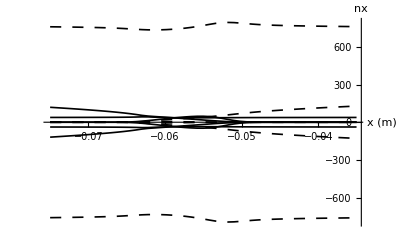

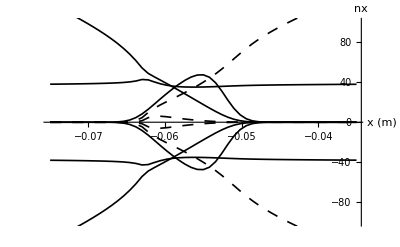

dataSet=DIII-D

ne0=3.×10^19

nsep=3.×10^18

B=1.9

freq=60

nz=2

etaList={1.,0.,0.,0.,0.}

TList={0.5,0.5,0.,0.,0.,0.}

modelList={2,2,0,0,0,0}

rmaj=1.67

rmin=0.68

rsep=0.65

sol=0.01

alphan=1.

alphaT=1.

```mathematica
g7=ComplexVectorListPlot[nxhot[1],"x (m)","nx"];g8=ComplexVectorListPlot[nxhot[2],"x (m)","nx"];g9=ComplexVectorListPlot[nxhot[3],"x (m)","nx"];g10=ComplexVectorListPlot[nxhot[4],"x (m)","nx"];
g11=ComplexVectorListPlot[nxhot[5],"x (m)","nx"];
g12=ComplexVectorListPlot[nxhot[6],"x (m)","nx"];
Show[{g7,g8,g9,g10,g11,g12},PlotRange->All]
Show[{g7,g8,g9,g10,g11,g12},PlotRange->{-100.,100}]
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

Seems to work ok.  Now should look at a real case.  I have no idea what the warm plasma root might be.  Or even it it' s real.  It doesn’t show up at all as related to a cold plasma resonance.

## Plot Profiles

```mathematica
Plot[nprof[x],{x,xmin,xmax}]
```

-Graphics-

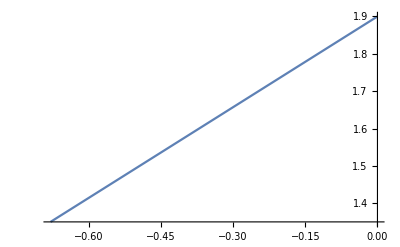

```mathematica
Plot[bprof[x],{x,xmin,xmax}]
```

```mathematica
Plot[tprof[x],{x,xmin,xmax}]
```

-Graphics-

## Initialization

#### Magnetic field,Density and Temperature Profiles

```mathematica
bprof[x_]:=If[Abs[(BXmax-BXmin)/BXmax]>10^-6,BXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(BXmax-BXmin),BXmin];
```

```mathematica
nprof[x_]:=If[Abs[(nXmax-nXmin)/nXmax]>10^-6,nXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(nXmax-nXmin),nXmin];
```

```mathematica
tprof[x_]:=If[Abs[(TXmax-TXmin)/TXmax]>10^-6,TXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(TXmax-TXmin),TXmin];
```